```mathematica
wg[c_,τ_,q_]:= KroneckerDelta[c,τ]/(q^2-1) -(1- KroneckerDelta[c,τ])/(q(q^2-1) );
wd[a_,τ_,q_,Γ_,p_]:= 
q p^2+(1-p)^2((1-Γ)^2 (q^2  KroneckerDelta[a,τ] +q (1-KroneckerDelta[a,τ] ))+(2Γ(1-Γ)+Γ^2)(q^2  KroneckerDelta[a,1]KroneckerDelta[τ,1]+ q*(1-KroneckerDelta[a,1]KroneckerDelta[τ,1])))
```

```mathematica
w3[a_,b_,c_,q_,Γ_,p_]:=wd[a,1,q,Γ,p] wd[b,1,q,Γ,p]wg[c,1,q^2]+wd[a,-1,q,Γ,p] wd[b,-1,q,Γ,p]wg[c,-1,q^2]
```

```mathematica
w3[1,1,1,2,0,p]
w3[1,-1,-1,2,0,p]
w3[-1,-1,1,2,0,p]
```

-1/60 (2 (1-p)^2+2 p^2)^2+1/15 (4 (1-p)^2+2 p^2)^2

1/20 (2 (1-p)^2+2 p^2) (4 (1-p)^2+2 p^2)

1/15 (2 (1-p)^2+2 p^2)^2-1/60 (4 (1-p)^2+2 p^2)^2

```mathematica
w3[1,-1,-1,q,Γ,p]-w3[-1,1,-1,q,Γ,p]
w3[1,-1,1,q,Γ,p]-w3[-1,1,1,q,Γ,p]
```

0

0

```mathematica
Series[wd[1,1,q,Γ,p],{Γ,0,2}]/.{q->2}
Series[wd[-1,1,q,Γ,p],{Γ,0,2}]/.{q->2}
Series[wd[1,-1,q,Γ,p],{Γ,0,2}]/.{q->2}
Series[wd[-1,-1,q,Γ,p],{Γ,0,2}]/.{q->2}
```

2 (2-4 p+3 p^2)+O[Γ]^3

2 (1-2 p+2 p^2)+O[Γ]^3

2 (1-2 p+2 p^2)+O[Γ]^3

2 (2-4 p+3 p^2)-4 (-1+p)^2 Γ+2 (-1+p)^2 Γ^2+O[Γ]^3

```mathematica
w000=w3[1,1,1,q,Γ,p];
w001=w3[1,1,-1,q,Γ,p];
w010=w3[1,-1,1,q,Γ,p];
w100=w3[-1,1,1,q,Γ,p];
w101=w3[-1,1,-1,q,Γ,p];
w011=w3[1,-1,-1,q,Γ,p];
w110=w3[-1,-1,1,q,Γ,p];
w111=w3[-1,-1,-1,q,Γ,p];
```

```mathematica
Series[w000,q-> Infinity]
Series[Expand[(q^2-2 p q^2+2 p^2 (1/2 q (1+q)+Γ^2))^2-(q^2-2 p q^2+2 p^2 (1/2 q (1+q)+Γ^2))^2/q^2,q],{q,0,6}]
```

Series[((q^2-2 p q^2+2 p^2 (1/2 q (1+q)+Γ^2))^2)/(-1+q^4)-((q-2 p q+p^2 (2 q-2 (-1+q) (Γ-Γ^2)))^2)/(q^2 (-1+q^4)),q→∞]

-(4 (p^4 Γ^4))/q^2-(4 (p^4 Γ^2))/q+(-p^4-4 p^2 Γ^2+8 p^3 Γ^2-4 p^4 Γ^2+4 p^4 Γ^4)+(-2 p^2+4 p^3-2 p^4+4 p^4 Γ^2) q+(-1+4 p-6 p^2+4 p^3+4 p^2 Γ^2-8 p^3 Γ^2+4 p^4 Γ^2) q^2+(2 p^2-4 p^3+2 p^4) q^3+(1-4 p+6 p^2-4 p^3+p^4) q^4+O[q]^7

```mathematica
Simplify[-((((1-p)^2 q+(2 (1-p) p+p^2) q) (1-Γ)^2+q Γ^2)^2)/(q^2 (-1+q^4))+((((1-p)^2 q^2+(2 (1-p) p+p^2) q^2) (1-Γ)^2+q Γ^2)^2)/(-1+q^4)]
```

(q^3 (-1+Γ)^4+(1-2 Γ+2 Γ^2)^2+q (1-2 Γ+2 Γ^2)^2+q^2 (-1+Γ)^2 (1-2 Γ+3 Γ^2))/(1+q+q^2+q^3)

```mathematica
M={{1,1,1,1,1,1,1,1},{1,1,1,-1,1,-1,-1,-1},{1,1,-1,1,-1,-1,1,-1},{1,-1,1,1,-1,1,-1,-1},{1,1,-1,-1,-1,1,-1,1},{1,-1,1,-1,-1,-1,1,1},{1,-1,-1,1,1,-1,-1,1},{1,-1,-1,-1,1,1,1,-1}};
MI = Inverse[M];
v= MI.Log[{w000,w001,w010,w100,w101,w011,w110,w111}];
vLegend={"h0","h1","h2","h3","J12","J23","J31","J123"};
```

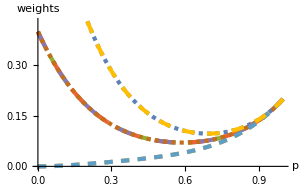

```mathematica
p1=Plot[Evaluate @ Table[Indexed[{w000,w001,w010,w100,w101,w011,w110,w111}/.{q->2,Γ->0},i],{i,8}],{p,0,1},AxesLabel->{"p","weights"},LabelStyle->{FontSize->22},PlotStyle->dashThick, PlotRange->Automatic,ImageSize->300]
Export["/Users/cathy/Google Drive/Random circuits/Pics/dephase_w3_Gamma0.png",Rasterize[p1,ImageResolution->150]];
```

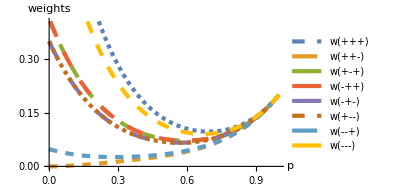

```mathematica
p2=Plot[Evaluate @ Table[Indexed[{w000,w001,w010,w100,w101,w011,w110,w111}/.{q->2,Γ->0.1},i],{i,8}],{p,0,1},PlotLegends->LineLegend[Automatic,{"w(+++)","w(++-)","w(+-+)","w(-++)","w(-+-)","w(+--)","w(--+)","w(---)"},Spacings->0.15],AxesLabel->{"p","weights"},LabelStyle->{FontSize->22},PlotStyle->dashThick, PlotRange->Automatic,ImageSize->300]
Export["/Users/cathy/Google Drive/Random circuits/Pics/dephase_w3_Gamma01.png",Rasterize[p2,ImageResolution->150]];
```

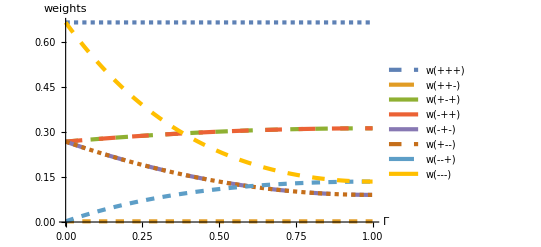

```mathematica
p3=Plot[Evaluate @ Table[Indexed[{w000,w001,w010,w100,w101,w011,w110,w111}/.{q->2,p->0.1},i],{i,8}],{Γ,0,1},PlotLegends->LineLegend[Automatic,{"w(+++)","w(++-)","w(+-+)","w(-++)","w(-+-)","w(+--)","w(--+)","w(---)"},Spacings->0.15],AxesLabel->{"Γ","weights"},LabelStyle->{FontSize->22},PlotStyle->dashThick, PlotRange->Automatic]
```

```mathematica
v[[]]
```

-1/8 Log[-((p^2 q+(1-p)^2 (q (1-Γ)^2+q (2 (1-Γ) Γ+Γ^2)))^2)/(q^2 (-1+q^4))+((p^2 q+(1-p)^2 (q^2 (1-Γ)^2+q (2 (1-Γ) Γ+Γ^2)))^2)/(-1+q^4)]-1/8 Log[((p^2 q+(1-p)^2 (q (1-Γ)^2+q (2 (1-Γ) Γ+Γ^2)))^2)/(-1+q^4)-((p^2 q+(1-p)^2 (q^2 (1-Γ)^2+q (2 (1-Γ) Γ+Γ^2)))^2)/(q^2 (-1+q^4))]+1/8 Log[-((p^2 q+(1-p)^2 (q (1-Γ)^2+q (2 (1-Γ) Γ+Γ^2)))^2)/(q^2 (-1+q^4))+((p^2 q+(1-p)^2 (q^2 (1-Γ)^2+q^2 (2 (1-Γ) Γ+Γ^2)))^2)/(-1+q^4)]+1/8 Log[((p^2 q+(1-p)^2 (q (1-Γ)^2+q (2 (1-Γ) Γ+Γ^2)))^2)/(-1+q^4)-((p^2 q+(1-p)^2 (q^2 (1-Γ)^2+q^2 (2 (1-Γ) Γ+Γ^2)))^2)/(q^2 (-1+q^4))]

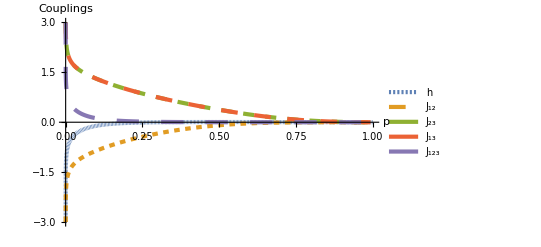

```mathematica
vNew = {v[[2]]+v[[3]]+v[[4]],v[[5]],v[[6]],v[[7]],v[[8]]};
vNewLegend={"h","J_12","J_23","J_13","J_123"};
dashThick=Transpose[{Table[AbsoluteDashing[i],{i,0,16,4}],
Table[AbsoluteThickness[3],{i,1,5}]}];
dephaseGamma001q2 = Plot[Evaluate @Table[Indexed[vNew/.{q->2,Γ->0.01},i],{i,5}],{p,0,1},PlotLegends->LineLegend[Automatic,vNewLegend,Spacings->0.15],AxesLabel->{"p","Couplings"},LabelStyle->{FontSize->22},PlotStyle->dashThick, PlotRange-> {{0,1},{-3,3}}]
Export["/Users/cathy/Google Drive/Random circuits/Pics/depolar_Gamma_001.png",Rasterize[dephaseGamma001q2,ImageResolution->150]];
```

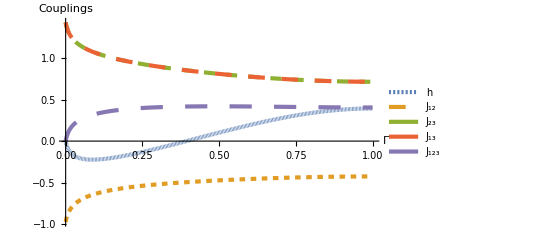

```mathematica
dephasep01q2 = Plot[Evaluate @ Table[Indexed[vNew/.{q->2,p->0.1},i],{i,5}],{Γ,0,1},PlotLegends->LineLegend[Automatic,vNewLegend,Spacings->0.15],AxesLabel->{"Γ","Couplings"},LabelStyle->{FontSize->22},PlotStyle->dashThick, PlotRange-> Automatic]
Export["/Users/cathy/Google Drive/Random circuits/Pics/depolar_p_01.png",Rasterize[dephasep01q2,ImageResolution->150]];
```

```mathematica
Transpose[{Table[AbsoluteDashing[i],{i,3,15,2}],
Table[AbsoluteThickness[5],{i,1,7}]}]
```

{{AbsoluteDashing[3],AbsoluteThickness[5]},{AbsoluteDashing[5],AbsoluteThickness[5]},{AbsoluteDashing[7],AbsoluteThickness[5]},{AbsoluteDashing[9],AbsoluteThickness[5]},{AbsoluteDashing[11],AbsoluteThickness[5]},{AbsoluteDashing[13],AbsoluteThickness[5]},{AbsoluteDashing[15],AbsoluteThickness[5]}}

```mathematica
Export["/Users/cathy/Google Drive/Random circuits/Pics/dephase_p_0.1_q2.png",Rasterize[dephasep01q2,ImageResolution->150]];
```

```mathematica
Directory[]
```

/Users/cathy